```mathematica
hif=Import[FileNameJoin[{NotebookDirectory[],"features/english_hindi.csv"}]];
frf=Import[FileNameJoin[{NotebookDirectory[],"features/english_french.csv"}]];
```

```mathematica
enumerate[l_]:=MapIndexed[{#2[[1]],#1}&,l]
```

```mathematica
markdowntable[mat_]:=TableForm[StringJoin@@Riffle[ConstantArray[" | ", Length@#+1],ToString/@#]&/@mat];
```

# Mutual Information/Feature Selection

```mathematica
Discretize[val_] := If[Chop[val] == 0, 0, Ceiling[val] ]
FrequencyPad[one_, two_]:= Module[{hash1, hash2, intersect},
hash1=Hash[#1[[1]]]->#1&/@one;
hash2=Hash[#1[[1]]]->#1&/@two;
intersect= hash1[[;;,1]]~Intersection~hash2[[;;,1]];
Return[{intersect/.hash1, intersect/.hash2}];
];
MutualInformation[features_, featurelabels_, col_]:=Module[{yprob,xprob,xyprob1, xyprob0,i},
(*yprob = p(y), xprob = p(x), xyprob1 = p(x|y=1), xyprob0= p(x|y=0) *)
yprob = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[Gather[featurelabels[[;;]] ] ];
xprob = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[Gather[Discretize/@features[[;;, col]] ] ];
xyprob1 = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[
Gather[Select[Transpose[{featurelabels}~Join~{Discretize/@features[[;;,col]]}], #1[[1]]==1&][[;;,2]]]
];
xyprob0 = Sort@Transpose@{#1[[;;,1]], Normalize[Length/@#1,Total]}&[
Gather[Select[Transpose[{featurelabels}~Join~{Discretize/@features[[;;,col]]}], #1[[1]]==0&][[;;,2]]]
];
Return[  yprob[[2,2]] * (xyprob1[[;;,2]].Log@xyprob1[[;;,2]]-#1[[1,;;,2]].Log@#1[[2,;;,2]]&[ FrequencyPad[xyprob1, xprob] ]) +
yprob[[1,2]] * (xyprob0[[;;,2]].Log@xyprob0[[;;,2]]-#1[[1,;;,2]].Log@#1[[2,;;,2]]&[ FrequencyPad[xyprob0, xprob] ])];
];
```

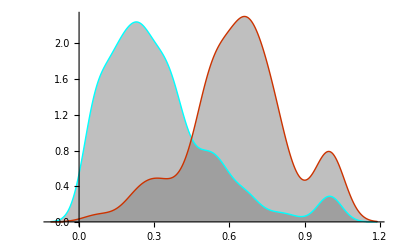

```mathematica
SmoothHistogram[
	Divide@@#&/@(#[[2;;,{17,1}]])&/@{frf,hif}
, Filling->Axis, PlotStyle->{Cyan,RGBColor[0.8,0.2,0]},FillingStyle->Directive[Opacity@0.5,Gray]
]
```

```mathematica
SortBy[#,-#[[2]]&]&@Table[{#3[[c]],N@MutualInformation[#1~Join~#2,ConstantArray[1,Length@#1]~Join~ConstantArray[0,Length@#2],c]},{c,1,Length@#1[[1]]}]&[hif[[2;;]],frf[[2;;]],hif[[1]]]//TableForm
```

markov_RR | 0.124757
num_reverse | 0.110777
depth | 0.10791
compressed_markov_RR | 0.101942
num_normal | 0.0988649
stdev_leaf_height | 0.0959409
compressed_num_nodes | 0.0838806
compressed_max_range_reverse | 0.0817872
max_range_reverse | 0.0817872
compressed_mean_inorder_pos_reverse | 0.078915
mean_inorder_pos_reverse | 0.078915
compressed_num_reverse | 0.0784315
compressed_reverse_max_depth | 0.0772467
mean_leaf_height | 0.0758574
compressed_mean_leaf_height | 0.0756852
compressed_length | 0.0707184
length | 0.0707184
compressed_depth | 0.0683356
num_nodes | 0.0674601
compressed_stdev_inorder_pos_reverse | 0.0639599
stdev_inorder_pos_reverse | 0.0639599
compressed_num_normal | 0.0624341
mean_range_reverse | 0.0623296
compressed_mean_range_reverse | 0.0620889
compressed_min_range_reverse | 0.0561532
reverse_max_depth | 0.0553115
stdev_range_reverse | 0.054712
compressed_stdev_range_reverse | 0.0479409
min_range_reverse | 0.0402458
compressed_stdev_leaf_height | 0.030288
compressed_markov_RN | 0.020526
markov_RN | 0.020526
markov_NN | 0.0189895
compressed_min_leaf_height | 0.0133551
compressed_markov_R | 0.0109877
markov_R | 0.0109877
compressed_markov_N | 0.00711246
markov_N | 0.00711246
compressed_markov_NN | 0.00552731
min_leaf_height | 0.00462757
compressed_markov_NR | 0.00123055
markov_NR | 0.00123055

# Logistic Regression

```mathematica
H[X_,θ_,hθ_] := Table[Sum[-X[[i,j]]X[[i,k]]hθ[X[[i]], θ](1-hθ[X[[i]], θ]),{i,1,Length[X]}], {j,1,Length[θ]},{k,1,Length[θ]}]
Delθ[X_,Y_,θ_,hθ_]:=Table[Sum[(Y[[i]]-hθ[X[[i]],θ])X[[i,j]],{i,1,Length[X]}],{j,1,Length[θ]}]
Newton[θ_,X_,Y_,hθ_]:= θ- Inverse[H[X,θ,hθ]].Delθ[X,Y,θ,hθ]
Newton[θ_,{X_,Y_,hθ_}]:= Newton[θ,X,Y,hθ]
```

```mathematica
Iterate[func_,n_,initial_,consts_]:=Module[{temp,i},
temp=initial;
For[i=0,i<n,i++,
 temp =func[temp,consts];
];
Return[temp];
];
```

```mathematica
XX=Table[Join[{1.},#[[i]]],{i,1,Length@#}]&@(hifeatures~Join~frfeatures);YY=ConstantArray[{1.}, Length@hifeatures]~Join~ConstantArray[{0.},Length@frfeatures];
```

```mathematica
Clear[sol]
sol[X_,Y_,θ_]:=Iterate[Newton, 100, θ, {X,Y,1/(1+ⅇ^(-#1.Flatten[#2]))&}]
```

```mathematica
sol[XX,YY,{0.,0.,0.}]
```

```mathematica
Show[
BubbleChart[{Flatten/@Tally@hifeatures,Flatten/@Tally@frfeatures}],
Plot[Solve[0.2542553502946426+-0.34731543843304x1+0.33441826042367423x2==0,x2][[1,1,2]],{x1,0,40},PlotStyle->Thick]
]
```

-Graphics-

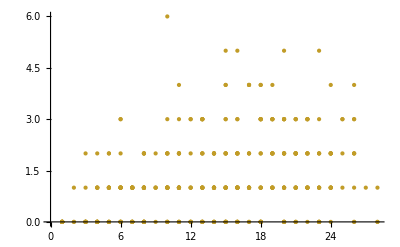

```mathematica
ListPlot@frf[[2;;,{4,5}]]
```

```mathematica
Norm[{1,1},10]
2^(1/10)
```

2^(1/10)

2^(1/10)

# Density Based Estimation

```mathematica
Clear@denseclassifier
denseclassifier[p_:10,k_:1,w_:0.2]:=With[{mins=Min/@Transpose@#,maxs=Max/@Transpose@#},Show[
ContourPlot[Norm[Exp[-k Norm[{x,y}-#]]&/@#,p]/Length[#]^(1/p),{x,mins[[1]]-(maxs-mins)[[1]]*w,maxs[[1]]+(maxs-mins)[[1]]*w},{y,mins[[2]]-(maxs-mins)[[2]]*w,maxs[[2]]+(maxs-mins)[[2]]*w},PlotLegends->Automatic,PlotRange->All, Contours->Table[0.05i,{i,0,20}]]
]]&;
```

```mathematica
Manipulate[denseclassifier[E^p,k][{{1,1},{3,4}}],{p,0,6},{k,0.1,5}]
```

```mathematica
denseclassifier[10,0.5][hif[[2;;,{1,17}]]]
denseclassifier[10,0.5][frf[[2;;,{1,17}]]]
```

-Graphics-

-Graphics-

# Topological Data Analysis

```mathematica
Needs["HierarchicalClustering`"]
```

### Functions

```mathematica
clusterorder::usage="clusterorder[dmat] rearranges the distancematrix to be in the order of a dendrogram created by the Agglomerate function. This is good to try an ";
clusterorder[dmat_]:=dmat[[ #,#]]&@ClusterFlatten@DirectAgglomerate[#,Linkage->"Ward"]&@dmat
```

```mathematica
dmat = DistanceMatrix@hif[[2;;]];
```

```mathematica
ArrayPlot[clusterorder@dmat,ColorFunction->Function[{z},GrayLevel[z^0.5]]]
```

DirectAgglomerate::ties: 5 ties have been detected; reordering input may produce a different result.

-Graphics-

```mathematica
Manipulate[Plot[Evaluate[(Juxt@@makebinfunc[n,o])@x],{x,0,1},PlotStyle->{Green,Red}],{n,Table[i,{i,5,15}]},{o, 0,0.5}]
```

```mathematica
Clear@Juxt
Juxt[fs__]:=With[{x=#},#@x&/@{fs}]&
```

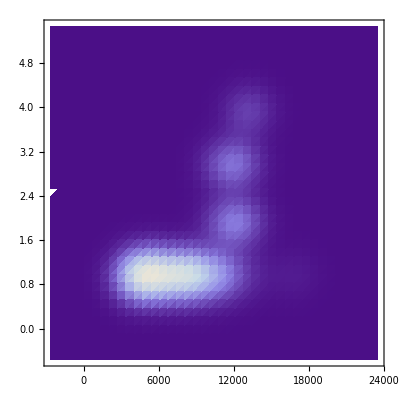

```mathematica
(* This is Cmax (max centrality). You can also use Mean, Geometric Mean, Harmonic Mean, etc *)
centrality[n_,distances_]:=Norm[distances,n] 
density[n_,k_,distances_]:=Norm[Exp[-k #]&/@distances,n]
SmoothDensityHistogram[Juxt[centrality[10,#]&,density[1,1,#]&]/@dmat,PlotRange->All]
```

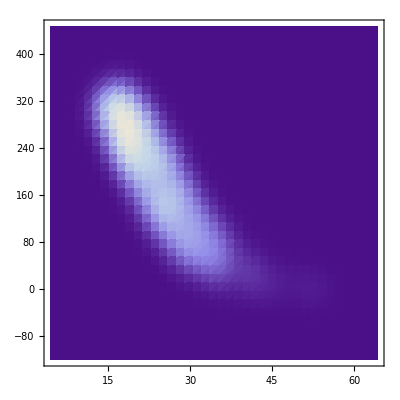
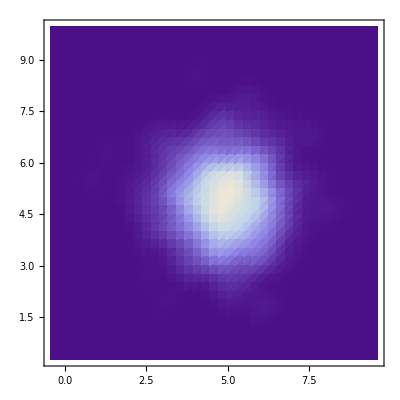

```mathematica
{
SmoothDensityHistogram[Juxt[centrality[Infinity,#]&,density[1,1,#]&]/@DistanceMatrix@#,PlotRange->All],
SmoothDensityHistogram[#,PlotRange->All]
}&@RandomVariate[NormalDistribution[5,1],{1000,2}]
```

```mathematica
GeneralClusterSplit[n_,cluster_]:=If[Head@cluster===Cluster,ClusterSplit[cluster,n],{cluster}];
GeneralClusterFlatten[c_]:=If[Head@c===Cluster, ClusterFlatten@c,If[Head@c===List,c,{ c}]];Clear@makebinfunc
makebinfunc[nbins_,overlap_]:=Juxt@@{Floor[nbins #]+1&, If[overlap /nbins - (nbins #-Floor[nbins #])/nbins >0,Floor[nbins #],Null]&}
```

```mathematica
Clear@AssignBins
AssignBins::usage="OverlappingBin[rows, metric, nbins, overlap] 
	rows: 2D list such that metric[[i]] is for row[[i]] 
	metric: some metric by which to bin the rows (eg, centrality) 
	nbins: number of bins to bin into
	overlap: fractional overlap of the bins, in both directions. range (0,1)
";
AssignBins[metric_, binfunc_]:= Select[Flatten[MapIndexed[With[{index=#2[[1]]},{index,#}&/@binfunc@#]&,metric],1],Not@SameQ[#[[-1]],Null]&]
CategoriesAndOverlaps [assignments_]:=Juxt[
{#[[1,2]],#[[;;,1]]}&/@GatherBy[#, #[[2]]&]&,
Juxt[#[[1,1]]&,#[[;;,2]]&]/@Select[GatherBy[#,First],Length@#>1&]&
]@assignments;
ClusteredBins[dfunc_,bins_,linkage_:"Ward"]:= MapAt[If[Head@#===Cluster,#,{#}]&@Agglomerate[#,DistanceFunction->(dfunc),Linkage->linkage ]&,#,2]&/@bins;
```

```mathematica
{bins,overlaps} =CategoriesAndOverlaps@AssignBins[Rescale[centrality[100,#]&/@dmat],makebinfunc[6, 0.5]];
(Length/@bins[[;;,2]])/Length@dmat//N
Length@overlaps/Length@dmat//N
groups=Quiet@ClusteredBins[(dmat[[ #1,#2 ]]&),bins];
clusters=(MapAt[GeneralClusterFlatten/@GeneralClusterSplit[3,#]&,#,2]&/@groups);
lookup=Dispatch[#[[1]]->#[[2]]&/@clusters];
idcluster=#[[1]]->#[[2]]&/@enumerate[Flatten[#,1]&@clusters[[;;,2]]];
clusterid = Dispatch[Reverse/@idcluster];
links=(With[{x=#},First@Select[#,MemberQ[#,First@x]&]/.clusterid&/@(x[[2]]/.lookup)]&/@overlaps);
Graph[idcluster[[;;,1]],#[[1]]<->#[[2]]&/@(DeleteDuplicates@links),VertexLabels->"Name",VertexSize->(MapAt[5 Length@#/Length@dmat&,#,2]&/@idcluster)]
```

{0.321839,0.149425,0.229885,0.275862,0.172414,0.229885,0.195402,0.0114943}

0.586207

-Graphics-

```mathematica
SmoothHistogram[#,PlotStyle->{Red}]&/@Transpose [
hif[[ 1 + Flatten[{11,8}/.idcluster] ]]
]
```